```mathematica
Ham = {{Ec/2+Ec*ng,-Ej/2,0},{-Ej/2,0,-Ej/2},{0,-Ej/2,Ec/2-Ec*ng}};
MatrixForm[Ham]
Eigenvalues[Ham/.{Ej->1,Ec->10}]
```

(Ec/2+Ec ng | -Ej/2 | 0
-Ej/2 | 0 | -Ej/2
0 | -Ej/2 | Ec/2-Ec ng)

{Root[5+(49-200 ng^2) #1-20 #1^2+2 #1^3&,1],Root[5+(49-200 ng^2) #1-20 #1^2+2 #1^3&,2],Root[5+(49-200 ng^2) #1-20 #1^2+2 #1^3&,3]}

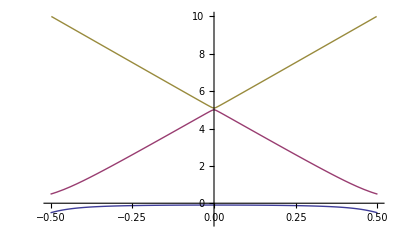

```mathematica
Plot[%,{ng,-.5,.5},PlotRange->{{-.5,.5},{-1,10}}]
```

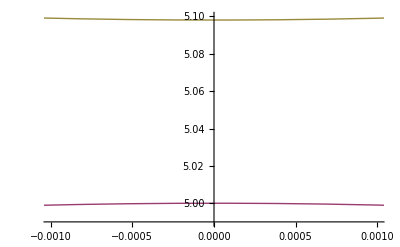

```mathematica
Plot[%%,{ng,-.5,.5},PlotRange->{{-.001,.001},{4.99,5.1}}]
```